## How To Mathematica (Semester 1):

To access a section, press the double arrow button.

### Shortcuts:

(For Mac I think it’s command instead of control)
For power, do Ctrl + 6
For fraction, do Ctrl + /
For square root, do Ctrl + 2

Escape symbols (Do escape then the word then escape again):
deg = °
pi = π
ee = ⅇ
dist = \[Distributed]
theta = θ
sum = ∑
sumt = ∑_(■=□)^□ □
un= ∪
inter = ∩
inf = ∞		
prodt = ∏_(■=□)^□ □
prod = ∏
dintt = ∫_■^□ □ⅆ□

### Define a function and use:

#### Variables

Variables can be defined with a single equals, assigning them to that symbol as long as the kernel is open (Mathematica being open).

```mathematica
x=2;(*Semicolon hides the output*)
```

```mathematica
3/x
```

3/2

```mathematica
Clear[x] (*Clears the variable if buggy*)
```

```mathematica
ClearAll["Global`*"] (*Clears the kernel*)
```

#### Replacing

Replace or /. can be used to quickly substitute a variable or anything in place of something else.

```mathematica
5+3x/.x->3(*Replace a variable*)
```

14

#### Defining/Differentiating/Integrating Functions

For simple mathematical functions, they are defined in the form:
f[x_]:= Whatever
If you want to use a trigonometric or logarithmic function, use square brackets.

```mathematica
f[x_]:=Sin[x](*Defines a function with an input x and some output*)
```

```mathematica
f'[x](*Derivative*)
```

Cos[x]

```mathematica
∫f[x]ⅆx (*Type escape intt escape for integral sign*)
```

-Cos[x]

#### Solving Equations

```mathematica
Solve[Sin[x]==0,x] (*When using trig or exponential functions, use square brackets and use reduce for periodic functions*)
```

{{x→ConditionalExpression[2 π C[1],C[1]∈ℤ]},{x→ConditionalExpression[π+2 π C[1],C[1]∈ℤ]}}

```mathematica
Solve[Log[x]==55,x]//N (*//N is the same as N[] but applies after the whole block*)
```

{{x→7.69479×10^23}}

```mathematica
Reduce[{f[x]==1,0<x<π},x] (*To solve trig equations, specify domain*)
```

x==π/2

```mathematica
g[x_]:=3 x^2+2x-5
s[x_]:=12x-4 x^2
```

```mathematica
Reduce[g[x]<s[x],x] (*Solve inequations without graphing*)
```

1/7 (5-2 √15)<x<1/7 (5+2 √15)

### Algebra:

#### Decimal Approximation and Absolute Value

To get a decimal approximation of a number, type N[item being evaluated, significant figures] or add //N at the of an expression when the number of significant figures isn’t relevant.

```mathematica
N[π/2,3]
π/2//N
```

1.57

1.5708

```mathematica
Abs[-5^2](*Absolute value function*)
```

25

#### Algebra Manipulation

```mathematica
Factor[x^3-x^2+x-1](*Factorise if possible*)
```

(-1+x) (1+x^2)

```mathematica
Expand[(x-1)(x^3-4x+5)]
```

-5+9 x-4 x^2-x^3+x^4

```mathematica
Solve[{x^2+5==y,5 x^2-10x==y},{x,y}]//N (*Solve for both x and y values as a system of equations*)
```

{{x→-0.427051,y→5.18237},{x→2.92705,y→13.5676}}

One can use Reduce to do “in terms of questions”, where in the example below I use it to reduce the equation down to only the solution for a. && means the statement in the brackets needs to be true, and the || operator means or the other must be true.

```mathematica
Reduce[d+x==x+b a-4a c,a]
```

(d==0&&b==4 c)||(b-4 c≠0&&a==d/(b-4 c))

```mathematica
Cancel[(x^3-x^2+x-1)/(x^2-1)](*To simplify a variable*)
```

(1+x^2)/(1+x)

```mathematica
Apart[(1+x^2)/(1+x)](*Partial fractions*)
```

-1+x+2/(1+x)

#### Finding Properties of Graphs/Equations

```mathematica
f[x_]:=x^3-2 x^2-x-5
```

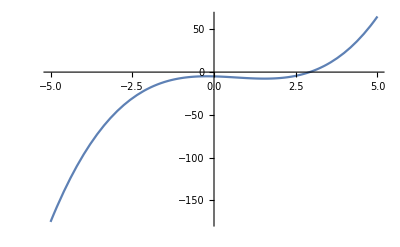

```mathematica
Plot[f[x],{x,-5,5}]
```

FindMinimum and FindMaximum can both take similar forms:
FindMinimum/Maximum[f[x],{x,lowBound,upperBound}]

```mathematica
FindMinimum[f[x],x](*Find Minimum works without any caveats*)
```

{-7.63113,{x→1.54858}}

```mathematica
FindMaximum[f[x],x](*Sometimes, findMaximum doesn't work so you will have to specify a range*)
```

{-4.88739,{x→-0.21525}}

```mathematica
FindMaximum[f[x],{x,-1,0}](*Apply a restriction from observing the plot, and inflection points*)
```

{-4.88739,{x→-0.21525}}

```mathematica
FindMinimum[f[x],{x,0,3}]
```

{-7.63113,{x→1.54858}}

Mathematica can determine the range, domain and period of a function like so:

```mathematica
FunctionDomain[√x,x]
```

x≥0

```mathematica
FunctionRange[Cos[x],x,y]
```

-1≤y≤1

```mathematica
FunctionPeriod[Tan[x],x]
```

π

### Plotting (2D):

#### Cartesian Plotting

The general form for plotting a function is:
Plot[{list or single equation without y==},{x,lowDomain,highDomain},PlotRange->{lowRange,highRange},AxesLabel -> {“xlabel”,”ylabel”},
Ticks -> {Range[lowDomain,highDomain,step up],Range[lowRange,highRange,step up}]

The Plot function doesn’t need to be this complicated unless the question asks for certain features.
The Range function generates a list of numbers between the low and high end of the number, while going up by the step count specified.

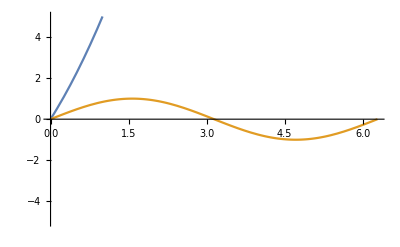

```mathematica
Plot[{x^2+4x,Sin[x]},{x,0,2Pi},PlotRange->{-5,5}] (*To plot multiple functions, use {} which are lists*)
```

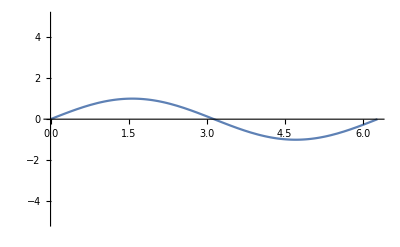

```mathematica
Plot[f[x],{x,0,2π},PlotRange->{-5,5}] (*When plotting, specify function, then domain and range.*)
```

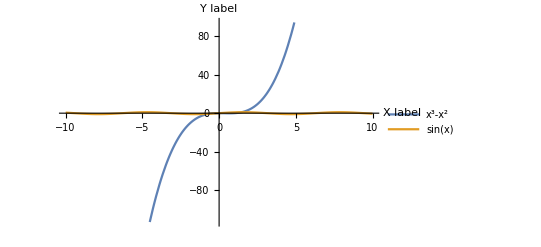

```mathematica
Plot[{x^3-x^2,Sin[x]},{x,-10,10},AxesLabel->{"X label","Y label"},PlotLegends->"Expressions"](*More options for plotting*)
```

```mathematica
Clear[x]
```

ContourPlot can be used to graph relations in any form. General syntax:
ContourPlot[{y=x},{x,lowBound,highBound},{y,lowBound,highBound},Axes->True]
They can be used to draw a vertical line, like so:

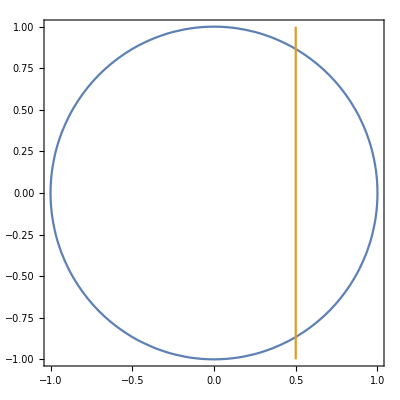

```mathematica
ContourPlot[{x^2+y^2==1,x==0.5},{x,-1,1},{y,-1,1},Axes->True]
```

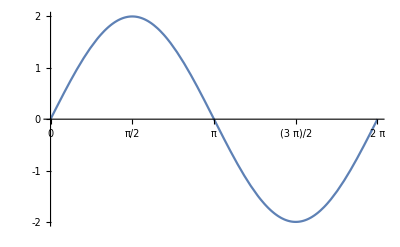

```mathematica
Plot[2Sin[x],{x,0,2Pi},PlotRange->{-2,2},Ticks->{Range[0,2Pi,Pi/2],Range[-2,2,1]}]  (*example of ticks*)
```

#### Polar Plotting

Polar functions can also be plotted as follows:

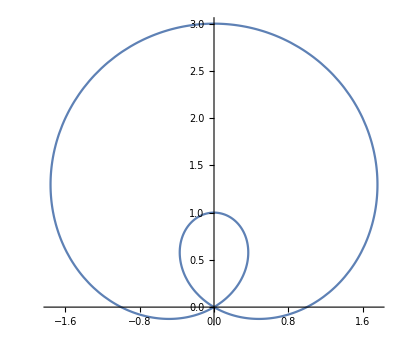

```mathematica
PolarPlot[2Sin[θ]+1,{θ,0,2Pi}]
```

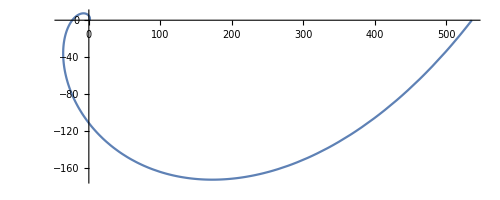

```mathematica
PolarPlot[E^θ,{θ,0,2π}]
```

### Calculus:

Note: For anyone outside of VCAA viewing this, this is about all the calculus students need to know because, according to VCAA, any other calculus is deemed “to hard” for us poor Australian high school students. We’ll all probably be tradies anyway what with our specialist mathematics skills. 

General syntax for calculus related functions:
Limit[f[x]->a, Direction -> “FromAbove” OR “FromBelow”]
D[f[x],x] for the derivative of a function
Integrate[f[x], {x,a,b}] evaluates a definite integral

```mathematica
g[x_]:=(x^3-x)/(x^2-1)
```

```mathematica
Limit[g[x],x->1](*to change to infinity, type  inf  without spaces.  is the character mathematica produces for escape*)
```

1

```mathematica
Limit[1/x,x->0,Direction->"FromAbove"] (*Choose the side to approach from*)
```

∞

```mathematica
D[2^x,x] (*Use D for single and multivariate calculus derivatives*)
```

2^x Log[2]

```mathematica
D[E^x+y^3,y]
```

3 y^2

```mathematica
Sin'''[x] (*Nesting derivatives, in this case Sine is derived three times*)
```

-Cos[x]

```mathematica
Integrate[E^(-x^2),x](*Indefinite Integral*)
```

1/2 √π Erf[x]

```mathematica
Integrate[E^(-x^2),{x,-∞,∞}](*Can integrate from infinity to negative infinity*)
```

√π

### Summation, Sequences & Series:

```mathematica
RecurrenceTable[{a[0]==1,a[1]==1,a[n]==a[n-1]+a[n-2]},a,{n,2,8}] (*Table up recurrence relation, give initial values and then specify values to go from and to*)
```

{2,3,5,8,13,21,34}

```mathematica
Sum[i^3,{i,1,n}](*Find a general formula of a sum, n is the end point and can be a real number just to see how values grow*)
```

1/4 n^2 (1+n)^2

```mathematica
Sum[1/n^2,{n,1,∞}](*Can also check if a sum converges*)
```

π^2/6

```mathematica
∑_(i=2)^n i(*Can also use  sum *)
```

1/2 (-2+n+n^2)

```mathematica
Product[i^2,{i,2,n}] (*Product can also be used in a similar fashion*)
```

(n!)^2

```mathematica
∏_(□=□)^□ □
```

You can also solve for the sequence of an equation with:
RSolve[{recurrence relation and initial conditions},function,variable]

```mathematica
RSolve[a[n]==a[n-1]+a[n-2]&&a[1]==1&&a[2]==1,a[n],n]
```

{{a[n]→Fibonacci[n]}}

```mathematica
RSolve[a[n]==2*a[n-1]&&a[1]==1,a[n],n]
```

{{a[n]→2^(-1+n)}}

### Matrices:

#### Defining Matrices

Matrices are represented as arrays (lists or {}) in Mathematica.

```mathematica
{{a,b},{c,d}}//MatrixForm(*2x2 Matrix*)
```

(a | b
c | d)

```mathematica
{a,b}//MatrixForm(*2x1 Matrix*)
```

(a
b)

```mathematica
{{a,b},{c,d}}//MatrixForm (*Use MatrixForm to convert to matrix shape*)
```

(a | b
c | d)

```mathematica
{{2,1,4},{1,4,6}}+{{7,1,0},{9,1,2}}//MatrixForm
```

(9 | 2 | 4
10 | 5 | 8)

```mathematica
MatrixForm[{{2,1,4},{1,4,6}}+{{7,1,0},{9,1,2}} ] (* matrixform shorthand is shown above, this is long hand *)
```

(9 | 2 | 4
10 | 5 | 8)

#### Manipulating Matrices

When multiplying two matrices, use the . symbol and not *. This is because of a difference in multiplication, where we have dot product and cross multiplication, google more if interested.

```mathematica
{x,y}.{{0,-3},{1,0}}//MatrixForm
```

(y
-3 x)

Transformation matrices can be made like so:

```mathematica
{{-2,0},{0,4}}.{x,y}+{3,5} (*Example of applying through transformations*)
```

{3-2 x,5+4 y}

You can then apply these transformations like so:

```mathematica
y==x^3/.{x->3-2 x,y->5+4 y}
```

5+4 y==(3-2 x)^3

And then solve for y:

```mathematica
Solve[5+4 y==(3-2 x)^3,y]
```

{{y→1/2 (11-27 x+18 x^2-4 x^3)}}

### Probability:

#### Factorial and Combinations

```mathematica
5!
```

120

N Choose C:

```mathematica
Binomial[n,c]
```

Binomial[n,c]

#### Distribution and Probability Command Manipulations

Binomial Distribution:
Pr(X == x) = nCx * p^x * (1-p)^(n-x)

```mathematica
BinomialDistribution[n,p]
```

```mathematica
Probability[x==2,x\[Distributed]BinomialDistribution[8,1/2]]//N
```

0.109375

A discrete plot can display the various values of the distribution.

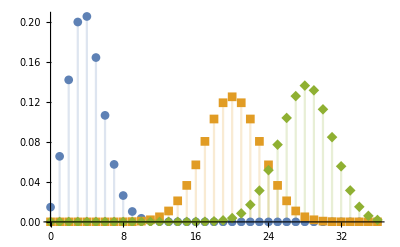

```mathematica
DiscretePlot[Table[PDF[BinomialDistribution[40,p],k],{p,{0.1,0.5,0.7}}]//Evaluate,{k,0,36},PlotRange->All,PlotMarkers->Automatic]
```

Hypergeometric Distribution (No replacement):

```mathematica
HypergeometricDistribution[trials,defectives/successes,total population]
```

```mathematica
Probability[x>2,x\[Distributed]HypergeometricDistribution[10,3,12]]
```

6/11

Normal Distribution:
NormalDistribution[] returns a distribution with μ = 0 and σ =1
Quantile returns the value that corresponds to the nth quantile. 0.6 = 60th

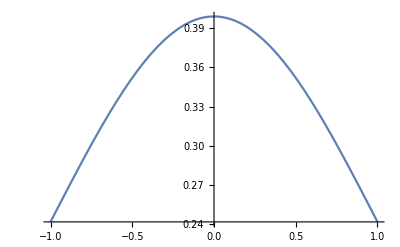

```mathematica
Plot[PDF[NormalDistribution[]][x],{x,-1,1}]
```

```mathematica
NormalDistribution[μ,σ]
```

```mathematica
Probability[x>2,x\[Distributed]NormalDistribution[0,1]]//N
```

0.0227501

```mathematica
Quantile[NormalDistribution[],0.6]//N
```

0.253347

To create continuous probability distributions with various functions like polynomials and exponentials:

```mathematica
ξ=ProbabilityDistribution[3 x^2,{x,0,1}](*Remember to evaluate this first*)
```

ProbabilityDistribution[3 x^2,{x,0,1}]

```mathematica
Probability[x>0.6,x\[Distributed]ξ]
```

0.784

Things like standard deviation, variance, expectation and mean can be calculated as follows:
Remember each of the distributions are it’s own distribution, including the probability distribution.

```mathematica
Expectation[2x+4,x\[Distributed]NormalDistribution[0,1]]
```

4

```mathematica
Variance[NormalDistribution[2,4]]
```

16

```mathematica
Mean[ProbabilityDistribution[3 x^2,{x,0,1}]]
```

3/4

```mathematica
StandardDeviation[BinomialDistribution[5,1/3]]
```

(√10)/3

Conditional probability can be done like:
x>3 \[Conditioned]x>2
do  cond

```mathematica
Probability[x>0.6\[Conditioned]x>0.2,x\[Distributed]ProbabilityDistribution[3 x^2,{x,0,1}]]
```

0.790323

### Variation:

```mathematica
dat={{5,4},{2,2},{10,20},{12,24}};
```

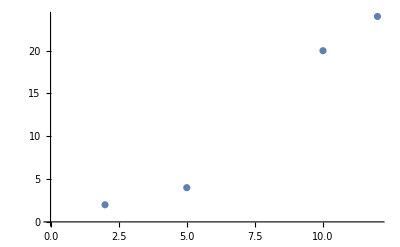

```mathematica
ListPlot[dat]
```

```mathematica
dato=Table[{x,x^3-2x},{x,0,10,0.2}]
```

{{0.,0.},{0.2,-0.392},{0.4,-0.736},{0.6,-0.984},{0.8,-1.088},{1.,-1.},{1.2,-0.672},{1.4,-0.056},{1.6,0.896},{1.8,2.232},{2.,4.},{2.2,6.248},{2.4,9.024},{2.6,12.376},{2.8,16.352},{3.,21.},{3.2,26.368},{3.4,32.504},{3.6,39.456},{3.8,47.272},{4.,56.},{4.2,65.688},{4.4,76.384},{4.6,88.136},{4.8,100.992},{5.,115.},{5.2,130.208},{5.4,146.664},{5.6,164.416},{5.8,183.512},{6.,204.},{6.2,225.928},{6.4,249.344},{6.6,274.296},{6.8,300.832},{7.,329.},{7.2,358.848},{7.4,390.424},{7.6,423.776},{7.8,458.952},{8.,496.},{8.2,534.968},{8.4,575.904},{8.6,618.856},{8.8,663.872},{9.,711.},{9.2,760.288},{9.4,811.784},{9.6,865.536},{9.8,921.592},{10.,980.}}

```mathematica
FindFormula[dato](*sometimes the function returns with hasthag, replace with an x*)  (*Beware, this function is more memory intensive*)
```

```mathematica
-2. #1+#1^3.&[x]
```

-2. x+x^3.

```mathematica
Fit[dato,{1,x,x^2,x^3},x](*Less memory intensive but not as accurate*)
```

-7.27016×10^-14-2. x-1.01507×10^-14 x^2+1. x^3

```mathematica
Normal[NonlinearModelFit[dato,a x^3+b x,{a,b},x]](*Normal produces a normal function*)
```

-2. x+1. x^3

### Differential equations:

Note: Differential Equations are not required knowledge by VCAA

With DSolve and NDSolve, the function can be tricky if you aren’t careful.

DSolve[{ODE,initial conditions},f[x],x]

For a numerical interpolating function (Fancy way of saying graph of pieced functions):
NDSolve[{ODE,initial conditions},f[x],{x,lowend,highend}]

Oscillation of a spring:

```mathematica
DSolve[{f''[x]+50/5 f[x]==0,
f[0]==5,
f'[0]==-3},
f[x],x]
```

{{f[x]→1/10 (50 Cos[√10 x]-3 √10 Sin[√10 x])}}

Object in free fall:

```mathematica
f[x]/.DSolve[{f''[x]==-9.8,f[0]==0,f'[0]==0},f[x],x]⟦1⟧
```

-4.9 x^2

```mathematica
sol=DSolveValue[y'[x]+y[x]==x&&y[0]==1,y[x],x]
```

ⅇ^-x (2-ⅇ^x+ⅇ^x x)

NDSolve uses interpolating functions to create a graphical plot of a function.

```mathematica
eqn=NDSolveValue[{y'[x]==Cos[x^2],y[0]==0},y[x],{x,-5,5}]
```

InterpolatingFunction[…][x]

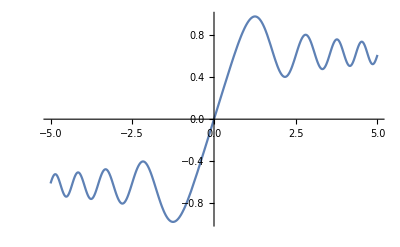

```mathematica
Plot[eqn,{x,-5.,5.}]
```

```mathematica
D[eqn,x](*Find derivative*)
```

InterpolatingFunction[…][x]

```mathematica
D[D[eqn,x],x](*Nest derivatives*)
```

InterpolatingFunction[…][x]

### Vectors:

Since vectors are a form of matrices, they are also represented as lists.
{i,j,k,...}

The previously mentioned matrix operations still hold from before, so remember to use . instead of *

```mathematica
a={-2,1}; (*Define a vector as -2i +j*)
b={1,4};
ab=b-a; (*Find AB*)
oa=a;
Solve[ab.(oa+t ab)==0,t](*Solve for perpendicular values*)
```

{{t→1/6}}

Arithmetic still follows under appropriate conditions, i.e same dimensions for addition and subtraction and the right row/column combination for multiplication.

```mathematica
2a
3a-4b
a.b
{{-1,2},{3,-4}}.{{-5,2},{2,4}}
```

{-4,2}

{-10,-13}

2

{{9,6},{-23,-10}}

Magnitudes and unit vectors can be computed as follows:

```mathematica
Norm[{√3,1}]
```

2

```mathematica
Normalize[{√3,1}]
```

{(√3)/2,1/2}

Euclidian distance of vectors:

```mathematica
EuclideanDistance[a,b]
```

3 √2

Find the angle between two vectors (gives you the result in radians by default):

```mathematica
VectorAngle[a,b]/°//N
```

77.4712

To plot vectors in Mathematica, use the following function:

```mathematica
VecPlot[vecs__?VectorQ]:=
Module[{vec},
vec=Arrow[{{0,0},#}]&/@vecs;
Graphics[vec,Axes->True, AxesLabel->{i,j},ImageSize->Large,Background->White]]
```

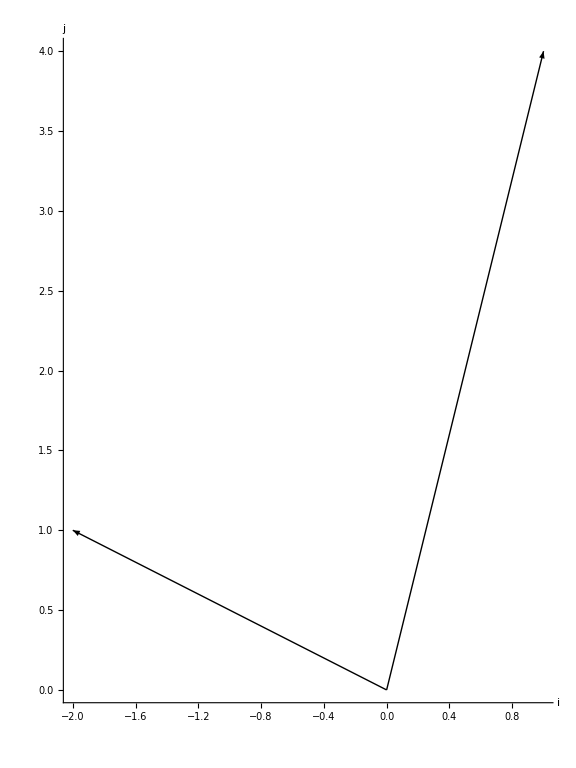

```mathematica
VecPlot[{a,b}]
```

To find the vector resolute of vector u onto v:

```mathematica
Projection[u,v]
Projection[{-2,3},{5,6}]
```

(v Conjugate[v].u)/(Conjugate[v].v)

{40/61,48/61}

```mathematica
A={-2,0};
B={8,11/2};
H={7,9/2};
R={2,2};
```

You can test for various properties such as being collinear like so:

```mathematica
Solve[A-B==k*(B-H),k]
Solve[A-B==k*(B-R),k]
Solve[A-R==k*(R-H),k]
```

{}

{}

{{k→4/5}}

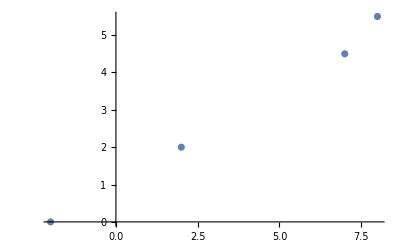

```mathematica
ListPlot[{A,B,H,R}] (*Can also plot*)
```

## How To Mathematica (Semester 2):

### Tips and Tricks:

#### Desmos-ish Plotter

If you ever look here, I made this really cool desmos ish interactive plotter.  Only problem is that you have to press somewhere outside or on the true/false button to update the graph.

```mathematica
Panel[DynamicModule[{f={x^3+x-6},a=-10,b=10,s=10,d=-10,pltRn=True},
Row[
{
Column[
Style[#,20]&/@
{Row[{"Functions: ",InputField[Dynamic[f],ContinuousAction->True]}],
Row[{"Automatic Plot Range:  ",Button[Dynamic[pltRn,ContinuousAction->True],pltRn=Not@pltRn]}],
Row[{"Dom: ",InputField[Dynamic[a],ContinuousAction->True]," to ",InputField[Dynamic[b],ContinuousAction->True]}],
Row[{"Ran: ",InputField[Dynamic[s],ContinuousAction->True]," to ",InputField[Dynamic[d],ContinuousAction->True]}]}],

Dynamic[
Plot[f,{x,a,b},ImageSize->Large,PlotRange->Evaluate@If[pltRn,Automatic,{s,d}]],ContinuousAction->True
]}]],ImageSize->Full]
```

#### Automatic Plotter

Also here’s an automatic plotter that will show all features VCAA requires of a graph, extremely useful for methods (n manipulates the distance the intercepts are shown):

```mathematica
UltraPlot[fx_,domL_,domH_,ranL_,ranH_,n_]:=
Module[{plt,sp,sparr,ep,eparr,xintercepts,xp,xparr,tp,tparr,tintercepts,epoints1,epoints2,yp,yparr,yintercepts,f},
plt=Plot[fx,{x,domL,domH},PlotRange->{ranL,ranH},ImageSize->Large];
yintercepts=If[0>domL&&0<domH, 
{yp=Graphics[Text[{0,Evaluate@(fx/.x->0)} ,{0+n,(fx/.x->0)-n}]];
yparr=Graphics[Arrow[{{0+n,(fx/.x->0)-n},{0,fx/.x->0}}]]},
{yp={};
yparr={}}];

sp=Graphics[Text[{domL,N@(fx/.x-> domL)} ,{domL+n,(fx/.x->domL)-n}]];
sparr=Graphics[Arrow[{{domL+n,(fx/.x->domL)-n},{domL,fx/.x->domL}}]];


epoints1={domL,fx/.x->domL};
epoints2={domH,fx/.x->domH};
ep=Graphics[Text[{domH,fx/.x->domH} ,{domH+n,(fx/.x->domH)-n}]];
eparr=Graphics[Arrow[{{domH+n,(fx/.x->domH)-n},{domH,fx/.x->domH}}]];

xintercepts=Solve[fx==0&&domL≤x≤domH,x]⟦All,1,2⟧;
xintercepts=Complement[xintercepts,epoints1,epoints2];
xp=Graphics[Text[{#,0} ,{#+n,0-n}]]&/@xintercepts;
xparr=Graphics[Arrow[{{#+n,0-n},{#,0}}]]&/@xintercepts;

tintercepts=Solve[D[fx,x]==0&&domL≤x≤domH,x]⟦All,1,2⟧;
tintercepts=Complement[tintercepts,epoints1,epoints2,Thread[{xintercepts,0}]~Delete~0];
tp=Graphics[Text[{#,fx/.x->#},{#+n,(fx/.x->#)-Sign[fx/.x->#]*n}]]&/@tintercepts;
tparr=Graphics[Arrow[{{#+n,(fx/.x->#)-Sign[fx/.x->#]*n},{#,fx/.x->#}}]]&/@tintercepts;

Show[{plt,sp,sparr,ep,eparr,xp,xparr,tp,tparr,yp,yparr},PlotRange->All]
]
Manipulate[UltraPlot[E^(-x^2),-1,1,-10,10,n],{n,0,2}]
```

#### Useful Shorthand to Blast through that tech active Exam

You can use single parameter functions or no parameter functions without square brackets like so:

```mathematica
N@√2
```

1.41421

```mathematica
RandomReal@{-1,1}
```

0.560793

You can retrieve your previously used command with control + L

You can apply a function to a list of items instead of individually applying the functions like so (/@):

```mathematica
N/@{E^2,I^I,Log[2],Cot[5]}
```

{7.38906,0.20788+0. ⅈ,0.693147,-0.295813}

You can quickly access your previous outputs with % like so:

```mathematica
Graphics@Disk[];
```

```mathematica
%
```

-Graphics-

You can also use Out[n] to get the nth output.

you can quickly retrieve the documentation of any function with ? followed by the function. You can press the arrow for the full page after.

```mathematica
?List
```

{e_1,e_2,…} is a list of elements.

```mathematica
?Graphics
```

Graphics[primitives,options] represents a two-dimensional graphical image.

Use NumberForm to approximate a number to some amount of decimal places like so:

```mathematica
NumberForm[N@√2,{∞,3}]
```

1.414

### Kinematics (Calculus):

For constant accelerated motion, the following formulas apply (That is a is a number other than 0, not  variable):
v = Final velocity
u = Initial velocity
x = Displacement
a = Acceleration
t = Time
------------------
x = ((u+v)t)/2
v = u + at
v^2=u^2+2ax
x = ut + at^2/2

In constant velocity, a = 0 and the other formula remain true, with a disappearing.

For variable acceleration:
Instantaneous Velocity at any time t (Gradient at some t): x’(t) = dx/dt(t)
Average Velocity over time intervals t0 and t: (x(t)-x(t0))/(t-t0) 
Instantaneous Acceleration at any time t (Gradient of vt graph at time t): x’’(t) = v’(t) = dv/dt(t)
Average Acceleration over time intervals t0 and t: (v(t)-v(t0))/(t-t0)

As for speed, it is distance/time, which is very different to displacement.
If it asks for the average speed, ALWAYS USE THE DEFINITE INTEGRAL to be safe, for example:
Find the average speed for the first three seconds:

```mathematica
f[t_]:=-t^2+4t+5
```

```mathematica
Integrate[Abs[f[x]],{x,0,3}]/(3-0)
```

8

When it asks for speed without average, it is the absolute value of the instantaneous velocity at that time t. Or |dx/dt(t)|
Another very common error is messing up the constant of integration.
Remember that integrating from a region GIVES THE CHANGE IN X, not the final x.
Δx = xFinal-xInitial
For example:
v(t) = 2-1/(t+1)^2 and x(0) = -3
Find the position after two seconds.

```mathematica
Integrate[2-1/(t+1)^2,{t,0,2}](*This calculates Δx from x = 0 to x =2 so it's x(2)-x(0) = Δx *)
```

10/3

We found Δx, and now need to calculate x(2). We know x(0) is -3 so:

Repeat the same thing for acceleration graphs with the area under the curve being Δv.

```mathematica
Solve[Δx==x2-x0,x2]/.{Δx->10/3,x0->-3}
```

{{x2→1/3}}

Area of a velocity graph is the distance, but the absolute value of the integral is the total distance covered. So, to find the distance covered in the first three seconds is the integral from the lower bound to the upper bound, without taking for account the constant as that is for position.

```mathematica
Integrate[Abs[2-1/(t+1)^2],{t,0,3}]
```

21/4

ALWAYS read if it asks for a decimal approximate or exact form. If it’s exact and you receive a surd, usually rationalize it.

### Circle Theorems:

Sine rule aka Lami’s theorem:a/Sin[α]=b/Sin[β]=c/Sin[Ω]
Cosine rule: a^2 = b^2+c^2 -2bc Cos[A]
Heron’s Formula: s = (a+b+c)/2
Area = √(S(S-A)(S-B)(S_C))

```mathematica
HeronArea[a_,b_,c_]:=
Module[{s},
s = (a+b+c)/2;
√(s(s-a)(s-b)(s-c))]
```

```mathematica
Solve[10/Sin[181Degree]==8/Sin[x Degree],x]
```

{{x→ConditionalExpression[(-ArcSin[(4 Sin[°])/5]+2 π C[1])/°,C[1]∈ℤ]},{x→ConditionalExpression[(π+ArcSin[(4 Sin[°])/5]+2 π C[1])/°,C[1]∈ℤ]}}

For this, a domain must be specified. You can use Reduce or Solve with an && statement to specify a domain.

```mathematica
Solutions=Solve[10/Sin[108Degree]==8/Sin[x ]&&0≤x≤2Pi,x]⟦All,1,2⟧//N
```

{2.27698,0.864615}

The above result is returned in radians. The ⟦All,1,2⟧ returns the solutions as numbers in a list for later use. 
For quickly convert between degrees and radians, you can use the following functions:

```mathematica
ToDeg[Radian_]:=
N@Radian*180/Pi
ToRad[Degree_]:=
N@Degree*Pi/180
```

/@ applies a function to a list, so you can convert multiple items.

```mathematica
ToDegree/@Solutions
```

{130.461,49.5388}

All the theorems:

### Circular Functions:

Shorthand function to convert to radians or degrees.

```mathematica
ToDeg[Radian_]:=
N@Radian*180/Pi
ToRad[Degree_]:=
N@Degree*Pi/180
```

Solve trig functions within a restricted domain:

```mathematica
Solve[Sin[x]==(√3)/2&&0≤x≤2Pi]
```

{{x→π/3},{x→(2 π)/3}}

General case solutions:

```mathematica
Solve[Sin[x]==(√3)/2]
```

{{x→ConditionalExpression[π/3+2 π C[1],C[1]∈ℤ]},{x→ConditionalExpression[(2 π)/3+2 π C[1],C[1]∈ℤ]}}

Inequalities work the same way, specify a restricted domain first:

```mathematica
Reduce[{Sin[x]<0,0<x<2Pi},x]
```

π<x<2 π

Plot a function with ticks for Pi etc:

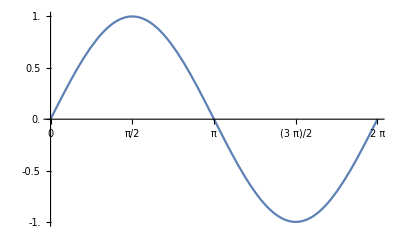

```mathematica
Plot[Sin[x],{x,0,2Pi},PlotRange->{-1,1},Ticks->{Range[0,2Pi,Pi/2],Range[-1,1,0.5]}]
```

### Complex numbers:

Real parts and imaginary parts of a number can be found like so:

```mathematica
z=(3-5I)/(2+I)
Re[z]
Im[z]
```

1/5-(13 ⅈ)/5

1/5

-13/5

Conjugate of a number:

```mathematica
Conjugate[z]
```

1/5+(13 ⅈ)/5

Get the argument and the distance of a number:
Note you may have to add a //Simplify at the end of Arg to evaluate the ArcTan fully.

```mathematica
Arg[z]
Abs[z]
```

-ArcTan[13]

√(34/5)

You can factor and solve equations over C with Extension -> I

```mathematica
Factor[ω^2+1,Extension->I]
```

(-ⅈ+ω) (ⅈ+ω)

```mathematica
Solve[ω^2+1==0,ω]
```

{{ω→-ⅈ},{ω→ⅈ}}

To convert to and from polar/exponential form:

```mathematica
ToPolarCoordinates[{Re[z],Im[z]}]
```

{2 √3,π/3}

```mathematica
FromPolarCoordinates[{2 √3,Pi/3}]
```

{√3,3}

## Chapter Summaries (Methods):

Graphing Techniques (Chapter 4, 5,7):

### -Graphics-

### -Graphics-

### -Graphics-

### -Graphics-

### -Graphics-

### -Graphics-

### -Graphics-

Polynomials and Cubics (Chapter 6):

### -Graphics-

### -Graphics-

### -Graphics-

Transformations and Matrices (Chapter 7):

### -Graphics-

### -Graphics-

### -Graphics-

### -Graphics-

### -Graphics-

### -Graphics-

Circular Functions/Trigonometry (Chapter 14):

### -Graphics-

### -Graphics-

### -Graphics-

### -Graphics-

### -Graphics-

### -Graphics-

### -Graphics-

### -Graphics-

### -Graphics-